## Miscellaneous explorations of model reduction. Section 6.5.2 (Balanced coordinates) Figure 6.7

```mathematica
Clear["Global`*"];
SetOptions[Plot,PlotRange -> All];
```

```mathematica
A1=({{-1, 0}, {0, -2}}); B1=({{1}, {1}}); C1=({{1, 2}});
Gss1=StateSpaceModel[{A1,B1,C1}]
```

-1010-21120StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[Gss1,s]
```

(4+3 s)/(2+3 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11421FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Apart[{{(4+3 s)/(2+3 s+s^2)}}]
```

{{1/(1+s)+2/(2+s)}}

```mathematica
atr=DiagonalMatrix[{A1[[1,1]]}];
btr=DiagonalMatrix[B1[[1]]];
ctr=DiagonalMatrix[{C1[[1,1]]}];
Gsstr1=StateSpaceModel[{atr,btr,ctr}]
```

-1110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
dres=DiagonalMatrix[-C1[[1,2]]/A1[[2,2]]*B1[[2]]];
Gssres1=StateSpaceModel[{atr,btr,ctr,dres}]
```

-1111StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
p1=ControllabilityGramian[Gss1];q1=ObservabilityGramian[Gss1];TraditionalForm/@{p1,q1}
```

{(1/2 | 1/3
1/3 | 1/4),(1/2 | 2/3
2/3 | 1)}

```mathematica
{tbal1,Gssbal1}=InternallyBalancedDecomposition[Gss1]//FullSimplify;
TraditionalForm /@ {tbal1,Gssbal1}
```

{(1/(√2) | -1/(√2)
1/2 | 1/2),-3/2-1/21+1/(√2)-1/2-3/21-1/(√2)1+1/(√2)1-1/(√2)0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
{abal1,bbal1,cbal1,dbal1}=Normal[Gssbal1]
```

{{{-3/2,-1/2},{-1/2,-3/2}},{{1+1/(√2)},{1-1/(√2)}},{{1+1/(√2),1-1/(√2)}},{{0}}}

```mathematica
atr1=DiagonalMatrix[{abal1[[1,1]]}];
btr1=DiagonalMatrix[bbal1[[1]]];
ctr1=DiagonalMatrix[{cbal1[[1,1]]}];
Gssbaltr1=StateSpaceModel[{atr1,btr1,ctr1}]
```

-3/21+1/(√2)1+1/(√2)0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
ares1=DiagonalMatrix[{abal1[[1,1]]-abal1[[1,2]]/abal1[[2,2]]*abal1[[2,1]]}]//FullSimplify;
bres1=DiagonalMatrix[{bbal1[[1,1]]-abal1[[1,2]]/abal1[[2,2]]*bbal1[[2,1]]}]//FullSimplify;
cres1=DiagonalMatrix[{cbal1[[1,1]]-cbal1[[1,2]]/abal1[[2,2]]*abal1[[2,1]]}]//FullSimplify;
dres1=DiagonalMatrix[{-cbal1[[1,2]]/abal1[[2,2]]*bbal1[[2,1]]}]//FullSimplify;
Gssbalres1=StateSpaceModel[{ares1,bres1,cres1,dres1}]
```

-4/32/3 (1+√2)2/3 (1+√2)1-(2 √2)/3StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel /@ {Gss1,Gsstr1,Gssres1,Gssbaltr1,Gssbalres1}
```

{(4+3 s)/(2+3 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11421FalseFalseFalseAutomaticNoneAutomatic,-1/(-1-s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11-1-11FalseFalseFalseAutomaticNoneAutomatic,(-2-s)/(-1-s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11-2-11FalseFalseFalseAutomaticNoneAutomatic,-(1+1/(√2))^2/(-3/2-s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111-31FalseFalseFalseAutomaticNoneAutomatic,(-4/3 (1-(2 √2)/3)-4/9 (1+√2)^2+(-1+(2 √2)/3) s)/(-4/3-s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11-4-41FalseFalseFalseAutomaticNoneAutomatic}

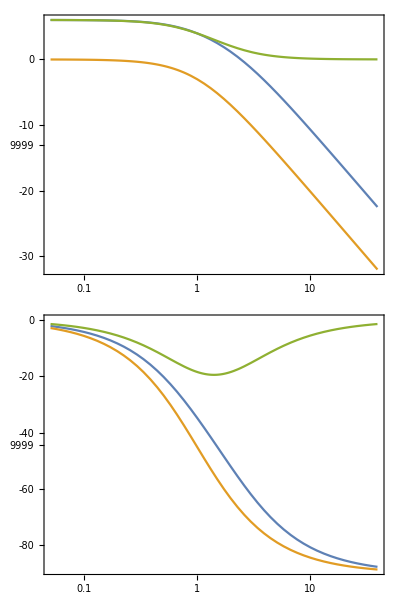
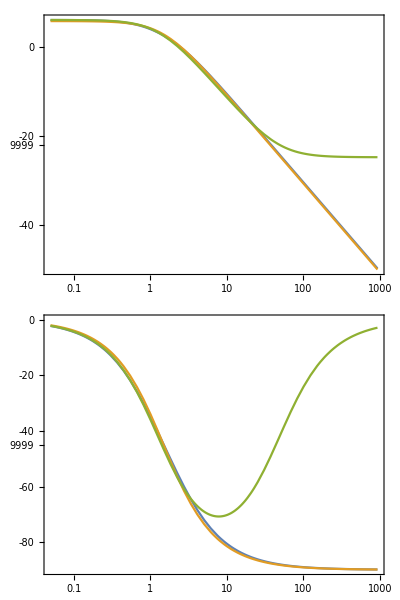

```mathematica
{BodePlot[{Gss1,Gsstr1,Gssres1}],BodePlot[{Gss1,Gssbaltr1,Gssbalres1}]}
```

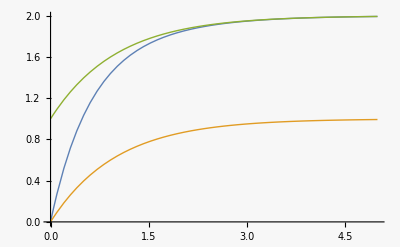
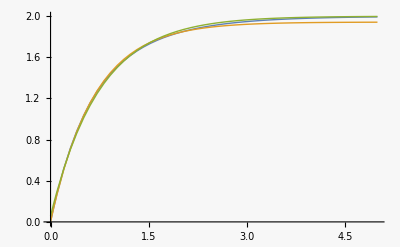

```mathematica
y1=OutputResponse[Gss1,UnitStep[t],t];
y2=OutputResponse[Gsstr1,UnitStep[t],t];
y3=OutputResponse[Gssres1,UnitStep[t],t];
y4=OutputResponse[Gssbaltr1,UnitStep[t],t];
y5=OutputResponse[Gssbalres1,UnitStep[t],t];
{Plot[{y1,y2,y3},{t,0,5}],Plot[{y1,y4,y5},{t,0,5}]}
```

```mathematica
p1bal=ControllabilityGramian[Gssbal1];
q1bal=ObservabilityGramian[Gssbal1];
TraditionalForm /@ {p1bal,q1bal}
```

{(1/6 (3+2 √2) | 0
0 | 1/6 (3-2 √2)),(1/6 (3+2 √2) | 0
0 | 1/6 (3-2 √2))}

```mathematica
Eigenvalues[Gssbal1[[1,1]]]
```

{-2,-1}

```mathematica
FullSimplify /@{y1,y2,y3,y4,y5}
```

{{ⅇ^-t (-1+Cosh[t]+3 Sinh[t]) UnitStep[t]},{(1-Cosh[t]+Sinh[t]) UnitStep[t]},{(2-Cosh[t]+Sinh[t]) UnitStep[t]},{1/3 (3+2 √2) ⅇ^(-3 t/2) (-1+ⅇ^(3 t/2)) UnitStep[t]},{1/3 (6-(3+2 √2) ⅇ^(-4 t/3)) UnitStep[t]}}

Look at 1d optimal Hankel approximant (computed in Scilab)

```mathematica
ah={{-√2}}; bh={{1+1/(√2)}}; ch={{2/3(1+√2)}};dh={{1/2-(√2)/3}};
Gssh=StateSpaceModel[{ah,bh,ch,dh}]
```

-√21+1/(√2)2/3 (1+√2)1/2-(√2)/3StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

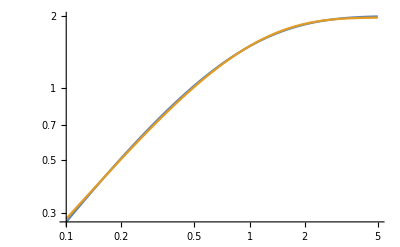

```mathematica
y6=OutputResponse[Gssh,UnitStep[t],t];
LogLogPlot[{y1,y6},{t,0.1,5}]
```

```mathematica
y6//FullSimplify
```

{1/6 (9+2 √2-2 (3+2 √2) ⅇ^(-√2 t)) UnitStep[t]}